```mathematica
a[n_]:=RandomChoice[{-1,1,0}]/n;
```

```mathematica
an=Table[a[n],{n,1,5000}];
```

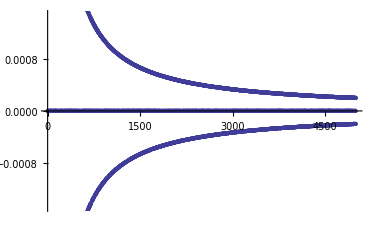

```mathematica
ListPlot[an]
```

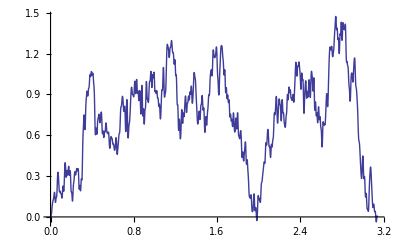

```mathematica
Plot[∑_(i=1)^500 (an[[i]] Sin[i x]),{x,0,π}]
```

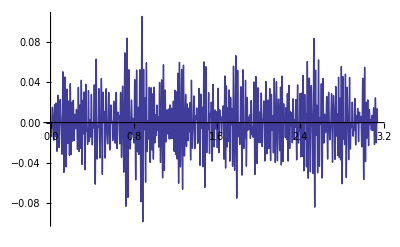

```mathematica
Plot[∑_(i=250)^500 (an[[i]] Sin[i x]),{x,0,π}]
```